# Практикум №6. Аналитическая геометрия в компьютерной среде

Выполнил студент ММФ  БГУ
КМ, 1 к, 3 гр . Шпак А . В .
 27 ноября 2021

## 1. Компьютерные модели аналитической геометрии.

Требуется спроектировать и построить математическую компьютерную сиситему, позволяющую решать задачи в области аналитической геометрии. Среда моделирования - символьный математический пакет Mathematica.
	Важно отметить, что это задание носит больше теоретический характер, нежели практический. Из-за этого в некоторых пунктах необходимость наличия стандартных ячеек Input/Output отпадает.

### Задание 1.0.

Необходимо спроектировать в Mathematica объекты системы «аналитическая геометрия на плоскости» и функции, позволяющие работать с этими объектами: отображать, вычислять свойства, управлять поведением объектов. Поэтому дальнейшее выполнение первого задания сводится к выполнению более локальных задач, которые я сформулирую и решу в этом параграфе.
	Пояснение:
	Для решения задач по аналитической геометрии сначала определюсь, с какими базовыми геометрическими объектами я буду работать. Прямая, точка, плоскость - первичные понятия. На их основе определяются луч, отрезок, ломаная линия, полигон.
	Каждое из перечисленных выше геометрических понятий буду ассоциировать в компьютерной среде соответствующим одноименным объектом.
	Объект в объектно-ориентированном проектировании – это сущность, характеризуемая состоянием (информация) и поведением (множество операций) для проверки и изменения этого состояния.
	Базовыми геометрическими объектами плоскости буду называть объекты точка и прямая. Двумерные объекты отрезок, многоугольник буду называть элементарными геометрическими объектами плоскости.
	Вводя в компьютерную среду новый объект, я должен научить Mathematica многому: во-первых, надо научить задавать экземпляр данного объекта, во-вторых надо где-то сохранять информацию о данном экземпляре объекта, в-третьих, понадобится извлекать свойства объекта, в-четвертых, хотелось бы иметь некоторый образ объекта.

### Задание 1.1.

Сформулировать основные принципы представления геометрического объекта в Mathematica.
	Пояснение:
	Для хранения информации об экземпляре объекта буду использовать понятие внутреннего представления объекта. 
	Внутреннее представление объекта – это информация об объекте, размещенная в структуре данных, которая используется в моделируемой компьютерной среде.
	Чтобы построить внутреннее представление объекта (или дать представление объекта в компьютерной среде) следует выявить информацию об объекте, выбрать структуру данных для ее хранения и разместить информацию об объекте в этой структуре.
	Представлением геометрического объекта буду называть выражение, которое имеет строго определенную голову и соответствующие этой голове аргументы.
	В отношении выражения представления геометрического объекта принимаю следующие соглашения: голова ObjectName представляемого объекта должна быть символом-атомом и вводимые символы ObjectName должны иметь смысловую нагрузку и иметь приставку-префикс km (kmPoint, kmVector, kmLine). 
	Символом в Mathematica называется атомарный (т. е. не составной, не распадающийся на части) поименованный объект, состоящий из конечной последовательности алфавитно-цифровых знаков, начиная с буквы или $, не содержащей специальных символов. Перечень специальных символов в Mathematica: знаки пунктуации, знаки операций и т. п.
	Спроектирую далее аргументы arg1, …, argN представления. Они должны представлять информацию об экземпляре объекта, необходимую и достаточную для его однозначной идентификации, удобную для вычисления его свойств и определения поведения. 
	Сначала выявлю такую общую информацию, которая необходима для представления любого геометрического объекта: и для точки, и для прямой, и для вектора.
	Первым аргументом arg1 в представлении будет символ km. Для разработчиков символ km, будучи первым аргументом выражения с головой kmObjectName, будет указывать, что данное выражение является представлением, Базой Знаний об объекте, в отличие от выражений-операторов, конструкторов объекта.
	Какую еще информацию удобно разместить в представлении объекта? При решении задач я зачастую именую точку, вектор, прямую. Поэтому вторым аргументом представления будет имя объекта, если объект именован. Имя логично указывать атомом типа String. Например, точку можно именовать ”A”, прямую – ”L1”. Если объект не именуется, второй аргумент будет представлен выражением вида ””.
	Следующие аргументы arg3, …, argN в представлении должны отражать базовые знания об экземпляре объекта, информацию для его однозначной идентификации, удобную для вычисления свойств объекта. На основании рассуждений, приведенных выше, можно детальнее указать метамодель для представления объектов «точка», «вектор», «прямая».

```mathematica
(*Представление объекта:*)
ObjectName[arg1,arg2,argN]
(*Показываю, что тип второго агрумента по умолчанию, если объект безымянный, тоже String:*)
""//Head
```

ObjectName[arg1,arg2,argN]

String

```mathematica
(*Метамодель для представления объектов «точка»,«вектор»,«прямая»:*)
kmObjectName[km,id_String,__]
(*kmObjectName - один из символов kmPoint, kmVector, kmLine.*)
(*km - аргумент–маркер, указывающий, что данное выражение является представлением объекта.*)
(*id_String – имя экземпляра объекта, если оно существует, или пустая строка вида ”” в противном случае.*)
```

kmObjectName[km,id_String,__]

### Задание 1.2.

Спроектировать в Mathematica возможность задания геометрического объекта различными способами.
	Пояснение:
	Сначала я определился с представлением объекта, но именно конструктор это представление задаст в тот момент, когда пользователь определится с данными в экземпляре объекта.
	Геометрический объект можно задавать различными способами. При задании объекта пользователь указывает данные, необходимые и достаточные для однозначного определения экземпляра объекта.
	Эти данные должны быть обработаны, преобразованы в информацию об объекте, которая, в свою очередь, будет сохранена в соответствующей структуре – так сформируется представление объекта. Наш замысел таков: пользователь задает экземпляр объекта любым корректным, оговоренным нами, общепринятым математическим способом. Mathematica же, получая эти данные, строит представление объекта. Чтобы построить представление объекта на основании указанных данных, создам функции-конструкторы объекта.
	Имена функций-конструкторов геометрического объекта я унифицирую: имя конструктора должно указывать объект, представление которого эта функция строит. Таким образом, для задания объекта я буду использовать оператор kmObjectName[_ _]. Его проектирую так, чтобы была возможность задания геометрических объектов различными способами.
	Оператор kmObjectName[_ _], аргументы которого – данные для построения объекта, преобразовывает эти данные во внутреннее представление. Таким образом, для конкретного объекта его представление и способ задания я связываю с одним единственным символом. Например, для объекта «точка» – с символом kmPoint.
	Итого: объект можно задавать различными способами. Для каждого из способов я описываю отдельный конструктор, но с одним и тем же символом, как если бы это было для функции. Передавая в качестве аргументов данные, я задействую определённый конструктор, чтобы сформировать представление объекта в системе и на выходе получаю экземпляр объекта. Представление так же можно построить напрямую, явно.

### Задание 1.3.

Спроектировать в Mathematica возможность извлечения свойств геометрического объекта.
 	Пояснение: 
 	Проектирую запросы для получения свойств объекта.
 	Как получить свойство объекта? Я должен это свойство запросить у Mathematica, Mathematica должна его вычислить и вернуть в качестве ответа на запрос. 
 	Как запросить свойство объекта, что нужно указать? Указать объект, свойство которого запрашиваю, и указать, какое свойство я запрашиваю. 
 	Как указать объект? Использовать его представление. 
 	Как указать конкретное свойство? Придумать для каждого свойства соответствующий идентификатор.
 	Введу следующие идентификаторы свойств объектов: ”id” – для запроса имени объекта, ”coord”– для запроса координат точки или вектора, ”equ”– для запроса общего уравнения прямой на плоскости.

```mathematica
(*Чтобы сформировать запрос о свойстве объекта, буду использовать выражение вида:*)
kmObjectName[km,id_String,__]["property"]
(*property - идентификатор запрашиваемого объекта.*)
(*Пример запроса каждого из свойств:*)
kmPoint[__]["id"]
kmPoint[__]["coord"]
kmVector[__]["id"]
kmVector[__]["coord"]
kmLine[__]["id"]
kmLine[__]["equ"]
```

kmObjectName[km,id_String,__][property]

kmPoint[__][id]

kmPoint[__][coord]

kmVector[__][id]

kmVector[__][coord]

kmLine[__][id]

kmLine[__][equ]

### Задание 1.4.

Спроектировать в Mathematica возможность отображения геометрического объекта. 
	Пояснение:
	Кроме создания объекта через констукторы или явно, формируя его представление в системе, а так же запроса свойств можно ещё и спроектировать возможность отображения геометрического объекта.
	Выделю два способа отображения объекта: в протоколе и на рисунке. 
	Под отображением объекта в протоколе будем понимать печать информации об объекте в выходной Out[]-ячейке. 
	Для реализации возможности отображения геометрического объекта на рисунке я научу Mathematica воспринимать конкретный геометрический объект как графический примитив двухмерной графики. А именно, я создам препроцессор kmGraphics2D к существующему в Mathematica оператору Graphics. Главной задачей препроцессора будет преобразование всех введенных мной объектов аналитической геометрии на плоскости в графические примитивы двумерной графики, понятные самой Mathematica.

## 2.1. Точка на плоскости. Представление и задание.

Создать в Mathematica подсистему для работы с точкой на плоскости: спроектировать внутреннее представление объекта «точка на плоскости», реализовать способы задания объекта, возможности извлечения его свойств, построения графического образа.
	Начну с представления и конструкторов.

### Задание 2.1.

Спроектируйте в Mathematica внутреннее представление объекта «точка на плоскости».

```mathematica
(*Представление объекта «точка на плоскости»:*)
kmPoint[km,id_String,coord:{_,_}]
(*coord - координаты точки в прямоугольной декартовой системе координат.*)
(*Объект - структура данных, в которой размещаются базовые знания о нём. Представление объекта и объект - синонимы. Экземпляр объекта - конкретная сущность.*)
```

kmPoint[km,id_String,coord:{_,_}]

### Задание 2.3.

Создайте конструктор объекта «точка на плоскости», требующий указания ее декартовых координат (прямоугольная декартова система координат).

```mathematica
(*Укажу в качестве единственного аргумента список вида
coord:{x,y},содержащий координаты точки в прямоугольной
декартовой системе координат*)
ClearAll[kmPoint]
(*Конструктор–оператор kmPoint, когда имя не задано, в декартовой системе координат.*)
kmPoint[coord:{_,_}]:=kmPoint[km,"",coord];
(*coord:{x,y} - список, содержащий координаты точки в прямоугольной декартовой системе координат.*)
(*Проверяю:*)
kmPoint[{2,3}]
kmPoint[{1,0}]
kmPoint[{1,1}]
```

kmPoint[km,,{2,3}]

kmPoint[km,,{1,0}]

kmPoint[km,,{1,1}]

### Задание 2.4.

Создайте возможность задания объекта «точка» путем указания ее имени и декартовых координат (прямоугольная декартова система координат).

```mathematica
kmPoint[id_String,coord:{_,_}]:=kmPoint[km,id,coord]
(*Проверяю:*)
(*Можно задать любое имя, так как строка:*)
myZeroPoint=kmPoint["Я нолик",{0,0}]
myHelloPoint=kmPoint["hello world",{1,1}]
(*Не забываю, что можно:*)
kmPoint[{2,3}]
```

kmPoint[km,Я нолик,{0,0}]

kmPoint[km,hello world,{1,1}]

kmPoint[km,,{2,3}]

### Задание 2.5.

Создайте возможность задания объекта «точка на плоскости» посредством указания ее полярных координат (согласованных с прямоугольной декартовой системой координат).

```mathematica
kmPoint[{ϕ_,ρ_},"pol"]:=kmPoint[km,"",{ρ Cos[ϕ],ρ Sin[ϕ]}]
(*Проверяю:*)
kmPoint[{Pi/3,2},"pol"]
kmPoint[{Pi/2,1},"pol"]
```

kmPoint[km,,{1,√3}]

kmPoint[km,,{0,1}]

### Задание 2.6.

Создайте возможность задания объекта «точка» посредством указания ее полярных координат (согласованных с прямоугольной декартовой системой координат) и, возможно, имени точки.

```mathematica
kmPoint[id_String,{ϕ_,ρ_},"pol"]:=kmPoint[km,id,{ρ Cos[ϕ],ρ Sin[ϕ]}]
(*Проверяю*)
kmPoint["my name",{Pi/6,3},"pol"]
kmPoint["not my name",{Pi/2,1},"pol"]
```

kmPoint[km,my name,{(3 √3)/2,3/2}]

kmPoint[km,not my name,{0,1}]

## 2.2. Точка на плоскости. Свойства и функции.

Реализую возможность извлечения свойств объекта точка на плоскости.

### Задание 2.7.

Напишите оператор, возвращающий имя объекта «точка», если оно существует.

```mathematica
kmPoint[km,id_String,__]["id"]:=If[id=="","Точка",id]
(*Проверяю:*)
kmPoint["A",{10,5}]["id"]
```

A

```mathematica
myZeroPoint["id"]
myHelloPoint["id"]
```

Я нолик

hello world

### Задание 2.8.

Напишите оператор, возвращающий декартовы координаты заданного объекта «точка на плоскости».

```mathematica
kmPoint[km,id_String,coord_List,___]["coord"]:=coord;
(*Проверяю*)
kmPoint[{Pi/4,1},"pol"]["coord"]
kmPoint["I am point",{Pi/2,1},"pol"]["coord"]
kmPoint[{22,22}]["coord"]
myZeroPoint["coord"]
myHelloPoint["coord"]
```

{1/(√2),1/(√2)}

{0,1}

{22,22}

{0,0}

{1,1}

```mathematica
(*И ещё один тест:*)
myPolarP=kmPoint[{Pi/3,2},"pol"]
myPolarP["coord"]
myPolarP["id"]
```

kmPoint[km,,{1,√3}]

{1,√3}

Точка

### Задание 2.9.

Постройте булеву функцию, позволяющую определить, имеет ли представленный объект «точка на плоскости» имя.

```mathematica
NamedQ[kmPoint[km,id_String,___]]^:=id!="";
(*Если точка будет именованным объектом, то вернётся True, иначе False.*)
(*Следует отметить,что при определении данного правила я использую оператор UpSetDelayed, который ассоциировал правило с
единственным аргументом функции NamedQ, точнее, с головой этого аргумента, c символом kmPoint. Проверю, какие правила на данном этапе проектирования ассоциированы с символом kmPoint:*)
?kmPoint
```

```mathematica
(*Введённые глобальные правила распределились по спискам следующим образом: DownValues - конструкторы, SubValues - запросы свойств, UpValues - функции, ассоциированные с помощью UpSetDelayed с kmPoint.*)
(*Не забываю про тесты:*)
NamedQ[myZeroPoint]
NamedQ[myHelloPoint]
NamedQ[kmPoint[{11,11}]]
```

True

True

False

## 2.3. Точка на плоскости. Отображение на рисунке.

Реализую возможность построения графического образа точки.

### Задание 2.11.

Три точки P1, P2, P3, заданные в прямоугольной декартовой системе координат соответственно координатами (−1, 0), (5, 3), (−2, 2). Представьте точки P1, P2, P3 в Mathematica, каждую как экземпляр объекта «точка на плоскости», и отобразите представленные точки в графической области.

```mathematica
(*Выполню требования задания: получу представление точек с помощью конструктора и ассоцтрую с соответствующими симоволами:*)
{P1,P2,P3}=kmPoint/@{{-1,0},{5,3},{-2,2}}
```

{kmPoint[km,,{-1,0}],kmPoint[km,,{5,3}],kmPoint[km,,{-2,2}]}

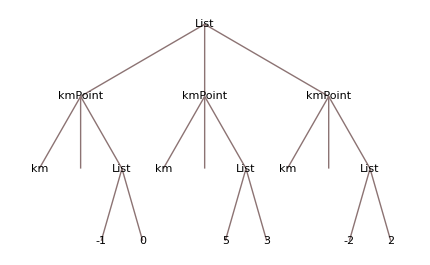

```mathematica
(*Список внутренних представлений точек в виде дерева:*)
{P1,P2,P3}//TreeForm
```

```mathematica
(*Оказывается каждая из точек не имеет имени (кроме как пустой строеи), потому как P1, P2, P3 - лишь символы, с которыми было ассоциировано внутреннее предмтавление.*)
(*Получаю координаты точек, формируя выражение, состоящее из чистой функции в связке с запросом и стандартным /@.*)
#["coord"]&/@{P1,P2,P3}
```

{{-1,0},{5,3},{-2,2}}

```mathematica
(*Оборачиваю выражение в примитив Point для получения уже графических объектов:*)
Point/@(#["coord"]&/@{P1,P2,P3})
```

{Point[{-1,0}],Point[{5,3}],Point[{-2,2}]}

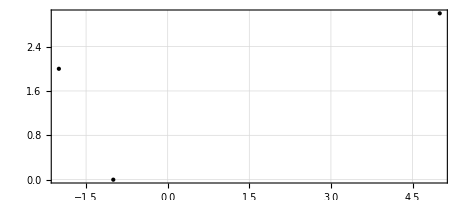

```mathematica
(*Отоображаю:*)
Graphics[Point/@(#["coord"]&/@{P1,P2,P3}),Frame->True,GridLines->Automatic]
```

```mathematica
(*Оформляю в виде функции(глобального правила преобразований):*)
ClearAll[kmGraphics2D];
kmGraphics2D[gp_List,opts___]:=Graphics[Point/@(#["coord"]&/@gp),opts]
(*Проверяю:*)
kmGraphics2D[{P1,P2,P3},Frame->True,GridLines->Automatic]
```

-Graphics-

## 2.4. Точка на плоскости. Задачи о точке.

### Задание 2.12.

Координаты точки M в полярной системе координат равны (5π/4, 1). 
a) Представьте точку М в Mathematica, используя конструктор объекта «точка на плоскости». 
b) Получите декартовы координаты точки М при условии, что начала координат совпадают, а полярная ось совпадает с положительной частью оси абсцисс. 
c) Получите имя точки. 
d) В графической области изобразите точку М зеленым цветом.

```mathematica
(*Задаю представление точки и ассоциирую с символом myPoint:*)
myMPoint=kmPoint["M",{(5Pi)/4,1},"pol"]
```

kmPoint[km,M,{-1/(√2),-1/(√2)}]

```mathematica
(*Получаю декартовы координаты:*)
myMPoint["coord"]
```

{-1/(√2),-1/(√2)}

```mathematica
(*Получаю имя точки:*)
myMPoint["id"]
```

M

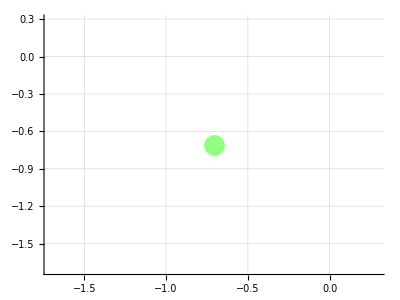

```mathematica
(*Можно написать явно выражение, которое отобразит мне точку:*)
Graphics[{AbsolutePointSize[15],Hue[0.31,0.5,1],Point[myMPoint["coord"]]},Axes->True,GridLines->Automatic]
```

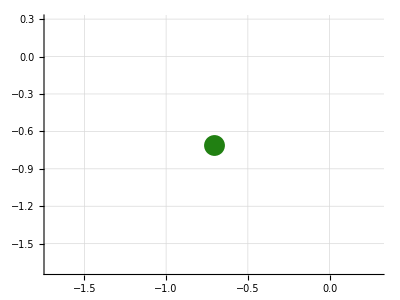

```mathematica
(*А можно написать свою функцию красивого отображения точки:*)
kmColorPoint[point_kmPoint,color_,opts___]:=Graphics[{AbsolutePointSize[15],color,Point[point["coord"]]},opts]
kmColorPoint[myPoint,Hue[0.31,0.86,0.5],Axes->True,GridLines->Automatic]
```

### Задание 2.13.

Напишите функцию, которая вычисляет координаты точки, делящей отрезок, заданный координатами своих концов, в отношении λ.

```mathematica
(*Пошагово опишу работу со списками из двух координат и как из этого могу вывести формулу:*)
A={xa,ya};
B={xb,yb};
A+B
```

{xa+xb,ya+yb}

```mathematica
A+λ B
```

{xa+xb λ,ya+yb λ}

```mathematica
(λ B+A)/(1+λ)
(*Таким образом могу получить готовую формулу без прикладывания усилий, например, к извлечению x и y из каждой точки.*)
```

{(xa+xb λ)/(1+λ),(ya+yb λ)/(1+λ)}

```mathematica
(*Тогда теперь могу написать функцию:*)
ClearAll[getLambdaCoords2]
getLambdaCoords2[pointA_kmPoint,pointB_kmPoint,λ_]:=kmPoint[(pointA["coord"] + λ pointB["coord"])/(λ + 1)]["coord"]
getLambdaCoords2[kmPoint[{11,1}],kmPoint[{-9,2}],5/3]
```

{-3/2,13/8}

### Задание 2.14.

Найдите расстояние между точками M и N, имеющими полярные координаты M(π/4, 3) и N(3π/4, 4). В графической области отобразите точку M красным цветом, точку N – синим, отрезок, их соединяющий – серым; при этом точку, расположенную дальше от полярной оси, отобразите большей по размеру, а также подпишите длину отрезка.

```mathematica
(*Задаю точки M и N:*)
myMPoint=kmPoint[{Pi/4,3},"pol"]
myNPoint=kmPoint[{(3Pi)/4,4},"pol"]
```

kmPoint[km,,{3/(√2),3/(√2)}]

kmPoint[km,,{-2 √2,2 √2}]

```mathematica
(*Выведу формулу вычисления расстояния пошагово:*)
B-A
```

{-xa+xb,-ya+yb}

```mathematica
(B-A)^2
```

{(-xa+xb)^2,(-ya+yb)^2}

```mathematica
Sqrt[(B-A)^2]
```

{√((-xa+xb)^2),√((-ya+yb)^2)}

```mathematica
(*Но мне нужен не список координат, а расстояние, поэтому использую функцию Dot для нахождения скалярного произведения:*)
(*Опять же, пошагово:*)
B.A
```

xa xb+ya yb

```mathematica
(*Но мне нужен не список, а расстояние, поэтому использую функцию Dot для нахождения скалярного произведения:*)
B-A
(B-A).(B-A)
```

{-xa+xb,-ya+yb}

(-xa+xb)^2+(-ya+yb)^2

```mathematica
(*Теперь легко получить формулу нахождения расстояния междк двумя точками:*)
Sqrt[(B-A).(B-A)]
```

√((-xa+xb)^2+(-ya+yb)^2)

```mathematica
Sqrt[#.#]&[pointN["coord"]-pointM["coord"]]
```

√((-3/(√2)-2 √2)^2+(-3/(√2)+2 √2)^2)

```mathematica
(*Функция нахождения расстояния между точками:*)
getDistBetwPoints[pointA_kmPoint,pointB_kmPoint]:=Sqrt[(pointB["coord"]-pointA["coord"]).(pointB["coord"]-pointA["coord"])]
(*И теперь считаю:*)
getDistBetwPoints[pointN,pointM]
```

5.

```mathematica
Head[5.]
```

Real

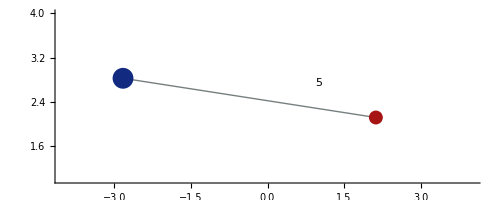

```mathematica
(*Строю график, в соответствии с требованиями условия:*)
Graphics[{Hue[0.5,0.07,0.5],Line[{pointM["coord"],pointN["coord"]}],AbsolutePointSize[10],Hue[0,0.88,0.65],Point[pointM["coord"]],AbsolutePointSize[15],Hue[0.63,0.86,0.5],Point[pointN["coord"]],Hue[0.5,0.5,0],Text[Style["5",Large],{1,2.75}]},PlotRange->{{-4,4},{1,4}},Axes->True]
```

### Задание 2.15

Дан треугольник А(0, 0), В(4, -3), С(12, 5). Вычислите координаты точки D пересечения биссектрисы внутреннего угла A с противолежащей стороной BC. Используйте свойство биссектрисы: точка D делит сторону BC в отношении λ = (длина АС)/(длина АВ).

```mathematica
(*Задаю точки:*)
myAPoint=kmPoint["A",{0,0}]
myBPoint=kmPoint["B",{4,-3}]
myCPoint=kmPoint["C",{12,5}]
```

kmPoint[km,A,{0,0}]

kmPoint[km,B,{4,-3}]

kmPoint[km,C,{12,5}]

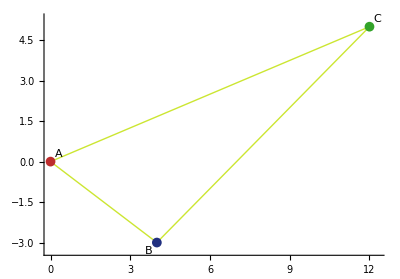

```mathematica
(*Решил нарисовать для красоты:*)
Graphics[{Hue[0.19,0.78,0.9],Line[{myAPoint["coord"],myBPoint["coord"],myCPoint["coord"],myAPoint["coord"]}],AbsolutePointSize[7],Hue[0,0.76,0.74],Point[myAPoint["coord"]],AbsolutePointSize[7],Hue[0.64,0.74,0.5],Point[myBPoint["coord"]],AbsolutePointSize[7],Hue[0.32,0.75,0.64],Point[myCPoint["coord"]],Hue[0.5,0.5,0],Text["A",myAPoint["coord"]+0.3],Hue[0.5,0.5,0],Text["B",myBPoint["coord"]-0.3],Hue[0.5,0.5,0],Text["C",myCPoint["coord"]+0.3]},PlotRange->All,Axes->True]
```

```mathematica
(*Необходимо найти точку пересечения биссектриссы с протеволежащей стороной.*)
(*Подсказка - использовать свойство биссектриссы. Что же, найдём наше лямбда по предложенной из условия формуле.*)
(*Функция для нахождения расстояния между двумя точками у меня есть из прошлого задания, поэтому остаётся только подставить точки:*)
myLambda=getDistBetwPoints[myAPoint,myCPoint]/getDistBetwPoints[myAPoint,myBPoint]
```

2.6

```mathematica
(*А готовая функцию, которая вычисляет координаты точки, делящей отрезок,заданный координатами своих концов,в отношении λ, у меня уже есть из задания 2.13, можно смело её воспользоваться, сразу создав новый экземпляр объекта точка:*)
myDPoint=kmPoint["D",getLambdaCoords2[myCPoint,myBPoint,myLambda]]
```

kmPoint[km,D,{6.22222,-0.777778}]

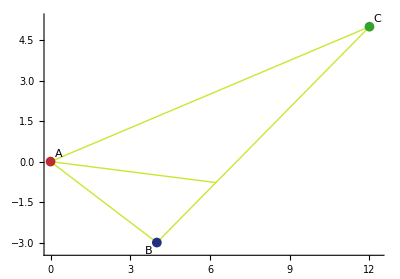

```mathematica
(*Можно нарисовать графически:*)
Graphics[{Hue[0.19,0.78,0.9],Line[{myAPoint["coord"],myBPoint["coord"],myCPoint["coord"],myAPoint["coord"]}],Line[{myAPoint["coord"],myDPoint["coord"]}],AbsolutePointSize[7],Hue[0,0.76,0.74],Point[myAPoint["coord"]],AbsolutePointSize[7],Hue[0.64,0.74,0.5],Point[myBPoint["coord"]],AbsolutePointSize[7],Hue[0.32,0.75,0.64],Point[myCPoint["coord"]],Hue[0.5,0.5,0],Text["A",myAPoint["coord"]+0.3],Hue[0.5,0.5,0],Text["B",myBPoint["coord"]-0.3],Hue[0.5,0.5,0],Text["C",myCPoint["coord"]+0.3]},PlotRange->All,Axes->True]
```

### Задание 2.16.

Вычислите полярные координаты вершин правильного шестиугольника, вписанного в окружность заданного радиуса. Расположите полюс в точке О, являющейся центром шестиугольника, а одну из вершин шестиугольника – на полярной оси при нулевом угле ее поворота. Изобразите вычисленные вершины, шестиугольник, описанную окружность. Напишите функцию, вычисляющую декартовы координаты вершин правильного n-угольника, вписанного в окружность заданного радиуса. Используйте метод построения вершин полигона в полярных координатах. Изобразите вычисленные вершины, полигон, описанную окружность.

```mathematica
(*Задаю радиус:*)
r=5;
(*Так как шестиугольник, то вот количество вершин:*)
n=6;
```

```mathematica
(*Список углов:*)
h=(2Pi)/n
ϕ=Range[0,2Pi,h]
```

π/3

{0,π/3,(2 π)/3,π,(4 π)/3,(5 π)/3,2 π}

```mathematica
(*Список полярных координат:*)
{#,r}&/@Range[0,2Pi,h]
```

{{0,5},{π/3,5},{(2 π)/3,5},{π,5},{(4 π)/3,5},{(5 π)/3,5},{2 π,5}}

```mathematica
myPoliarPoints=kmPoint[#,"pol"]&/@({#,r}&/@Range[0,2Pi,h])
```

{kmPoint[km,,{5,0}],kmPoint[km,,{5/2,(5 √3)/2}],kmPoint[km,,{-5/2,(5 √3)/2}],kmPoint[km,,{-5,0}],kmPoint[km,,{-5/2,-(5 √3)/2}],kmPoint[km,,{5/2,-(5 √3)/2}],kmPoint[km,,{5,0}]}

```mathematica
(*А теперь отобразим графически:*)
(*Как обычно пошагово составное выражение:*)
(*Так я получу список координаток:*)
#["coord"]&/@Table[myPoliarPoints[[i]],{i,1,Length[myPoliarPoints]}]
```

{{5,0},{5/2,(5 √3)/2},{-5/2,(5 √3)/2},{-5,0},{-5/2,-(5 √3)/2},{5/2,-(5 √3)/2},{5,0}}

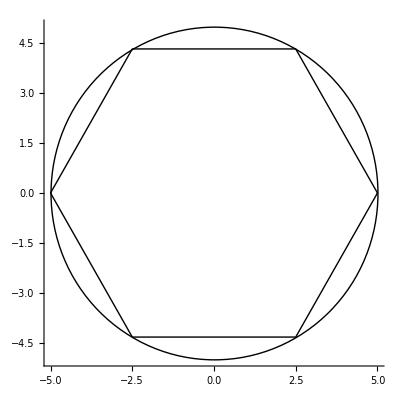

```mathematica
(*Предлагаю построить графически:*)
Graphics[{Circle[{0,0},r],Line[#["coord"]&/@Table[myPoliarPoints[[i]],{i,1,Length[myPoliarPoints]}]]},Axes->True]
```

```mathematica
(*Напишу функцию,вычисляющую декартовы координаты вершин правильного n-угольника,вписанного в окружность заданного радиуса:*)
Decart[n_,radius_]:=#["coord"]&/@Table[(kmPoint[#,"pol"]&/@({#,radius}&/@Range[0,2Pi,(2Pi)/n]))[[i]],{i,1,n+1}]
(*Проыеряю:*)
Decart[6,5]
```

{{5,0},{5/2,(5 √3)/2},{-5/2,(5 √3)/2},{-5,0},{-5/2,-(5 √3)/2},{5/2,-(5 √3)/2},{5,0}}

{{7,0},{7/(√2),7/(√2)},{0,7},{-7/(√2),7/(√2)},{-7,0},{-7/(√2),-7/(√2)},{0,-7},{7/(√2),-7/(√2)},{7,0}}

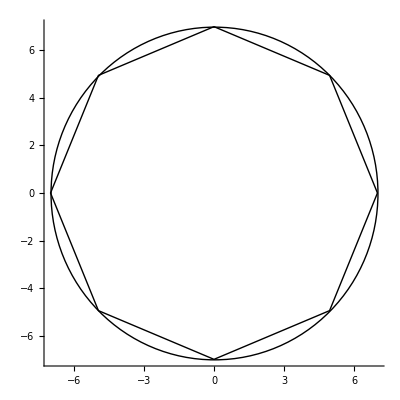

```mathematica
(*Ну и ещё раз проверяю:*)
Decart[8,7]
(*Ну и для проверки работы попробую построить:*)
Graphics[{Circle[{0,0},7],Line[Decart[8,7]]},Axes->True]
```

{{10,0},{10 Cos[(2 π)/9],10 Sin[(2 π)/9]},{10 Sin[π/18],10 Cos[π/18]},{-5,5 √3},{-10 Cos[π/9],10 Sin[π/9]},{-10 Cos[π/9],-10 Sin[π/9]},{-5,-5 √3},{10 Sin[π/18],-10 Cos[π/18]},{10 Cos[(2 π)/9],-10 Sin[(2 π)/9]},{10,0}}

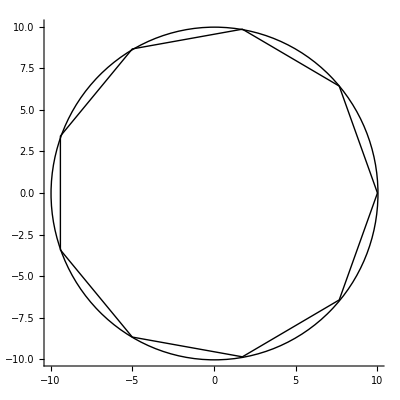

```mathematica
(*И ещё раз проверю:*)
Decart[9,10]
(*Ну и для проверки работы попробую построить:*)
Graphics[{Circle[{0,0},10],Line[Decart[9,10]]},Axes->True]
```